```mathematica
Rawdata = Import[NotebookDirectory[]<>"soeren_kress_HTS.lvm"];
```

```mathematica
Messpaare = ToExpression@StringSplit[Flatten[Drop[Rawdata, 22]]];
```

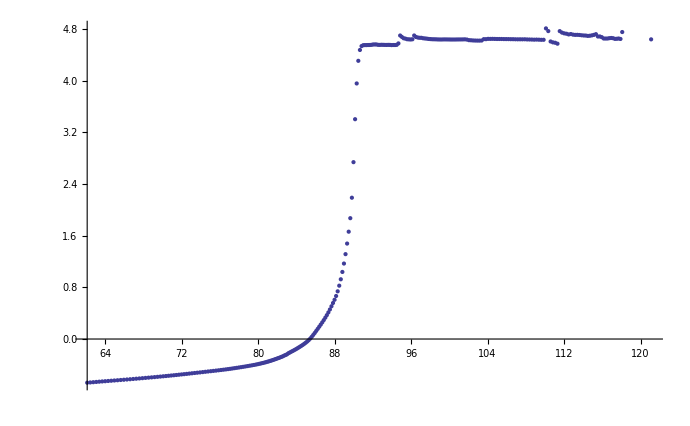

```mathematica
ListPlot[Messpaare, Joined->False]
```

```mathematica
Messpaare
```

{{121.094966,4.640790},{118.073357,4.754160},{117.890060,4.647010},{117.696745,4.653810},{117.509789,4.649780},{117.317594,4.648190},{117.124828,4.658240},{116.931250,4.661900},{116.732676,4.658970},{116.540344,4.653700},{116.339315,4.653300},{116.139743,4.653850},{115.934828,4.674940},{115.731253,4.685490},{115.529850,4.685150},{115.323587,4.721230},{115.115197,4.710000},{114.905526,4.702690},{114.690632,4.696750},{114.476726,4.694360},{114.261300,4.699530},{114.047575,4.700790},{113.825888,4.703880},{113.605307,4.708340},{113.381184,4.710780},{113.156854,4.710020},{112.931604,4.713720},{112.703651,4.722710},{112.474419,4.716940},{112.243795,4.727780},{112.011063,4.733710},{111.776458,4.745440},{111.539988,4.768090},{111.303198,4.573560},{111.065735,4.588060},{110.824736,4.594220},{110.584251,4.607870},{110.341784,4.768730},{110.098407,4.810650},{109.854591,4.634120},{109.609154,4.633640},{109.364112,4.635460},{109.117804,4.637350},{108.870945,4.635880},{108.624957,4.637630},{108.378893,4.638580},{108.132396,4.639450},{107.885820,4.641800},{107.639757,4.641100},{107.394099,4.641570},{107.149070,4.641240},{106.904560,4.641870},{106.661516,4.643310},{106.418750,4.643520},{106.177799,4.644480},{105.936298,4.644830},{105.696619,4.645120},{105.457806,4.646290},{105.220930,4.646370},{104.984212,4.646330},{104.749314,4.647440},{104.515754,4.648650},{104.283651,4.647910},{104.052182,4.648420},{103.823475,4.643720},{103.596930,4.643950},{103.371372,4.622600},{103.147629,4.621310},{102.925575,4.621540},{102.704501,4.622290},{102.484882,4.623660},{102.266718,4.626400},{102.053787,4.628150},{101.839591,4.637310},{101.624246,4.641010},{101.413308,4.639930},{101.203933,4.639450},{100.995896,4.639330},{100.791789,4.639040},{100.587355,4.638320},{100.380585,4.638360},{100.178433,4.638240},{99.980217,4.638930},{99.777056,4.639310},{99.577732,4.639810},{99.379766,4.639640},{99.182419,4.638590},{98.985807,4.638820},{98.790278,4.639500},{98.595360,4.641120},{98.401278,4.641890},{98.208337,4.642410},{98.016309,4.644750},{97.824786,4.647410},{97.633823,4.651950},{97.444351,4.654690},{97.255001,4.657820},{97.066937,4.664910},{96.879004,4.665150},{96.691687,4.669190},{96.505620,4.677220},{96.319870,4.700670},{96.134735,4.641820},{95.950112,4.638800},{95.766220,4.640940},{95.583043,4.642680},{95.399666,4.652520},{95.216918,4.657530},{95.034947,4.678270},{94.853257,4.700340},{94.672675,4.578000},{94.492541,4.555560},{94.312910,4.552960},{94.133507,4.553300},{93.954793,4.551890},{93.776162,4.554780},{93.598557,4.555400},{93.421045,4.554150},{93.243990,4.554870},{93.067428,4.555930},{92.891408,4.556800},{92.716149,4.554810},{92.541304,4.555940},{92.367155,4.561810},{92.193448,4.561820},{92.020183,4.561020},{91.846996,4.555860},{91.674245,4.553460},{91.501645,4.553160},{91.329750,4.551980},{91.158799,4.551830},{90.988098,4.550260},{90.817859,4.536700},{90.648013,4.476240},{90.478768,4.308360},{90.310366,3.957730},{90.141964,3.404190},{89.974324,2.738952},{89.806751,2.188354},{89.639922,1.871479},{89.473267,1.662206},{89.307080,1.478303},{89.141662,1.314468},{88.976470,1.168833},{88.811714,1.038864},{88.647540,0.925254},{88.484009,0.826157},{88.320581,0.738601},{88.157536,0.666180},{87.995096,0.608039},{87.832583,0.557838},{87.671001,0.507171},{87.509147,0.457887},{87.348298,0.412353},{87.188016,0.369971},{87.028340,0.330968},{86.869056,0.293475},{86.709840,0.258091},{86.550783,0.223571},{86.392679,0.190522},{86.234621,0.157667},{86.077222,0.125260},{85.920242,0.093397},{85.763558,0.062886},{85.607491,0.033871},{85.451840,0.007037},{85.296884,-0.016966},{85.142157,-0.037453},{84.987858,-0.056240},{84.833998,-0.073640},{84.680554,-0.090054},{84.527276,-0.105196},{84.375023,-0.119524},{84.222834,-0.133582},{84.071737,-0.147206},{83.920728,-0.160112},{83.769819,-0.172562},{83.619404,-0.184932},{83.469427,-0.196795},{83.319935,-0.208669},{83.170436,-0.219851},{83.021818,-0.236691},{82.874058,-0.247230},{82.726220,-0.256985},{82.578900,-0.267951},{82.432168,-0.277218},{82.286037,-0.285913},{82.139968,-0.294013},{81.994477,-0.301805},{81.848976,-0.309523},{81.705183,-0.317386},{81.561080,-0.324807},{81.416713,-0.332042},{81.271490,-0.338947},{81.122847,-0.345579},{80.971403,-0.352213},{80.815505,-0.358718},{80.654996,-0.365230},{80.488253,-0.371601},{80.314983,-0.377634},{80.134986,-0.383975},{79.946623,-0.390199},{79.750800,-0.396348},{79.547190,-0.402127},{79.336844,-0.407833},{79.120684,-0.413509},{78.899689,-0.419217},{78.675247,-0.424869},{78.448231,-0.430441},{78.219745,-0.435826},{77.991010,-0.441065},{77.763186,-0.446288},{77.536311,-0.451243},{77.310825,-0.456407},{77.084946,-0.461460},{76.856060,-0.465980},{76.620969,-0.470577},{76.377431,-0.475092},{76.125068,-0.479650},{75.864764,-0.484460},{75.598323,-0.489099},{75.326537,-0.493684},{75.050454,-0.498186},{74.771337,-0.502752},{74.490699,-0.507525},{74.208340,-0.512232},{73.925906,-0.517077},{73.643976,-0.521703},{73.362851,-0.526097},{73.084339,-0.530687},{72.808526,-0.535389},{72.535770,-0.539951},{72.264152,-0.544276},{71.993345,-0.548412},{71.723568,-0.552694},{71.454430,-0.557086},{71.185050,-0.561126},{70.915683,-0.565123},{70.643502,-0.569180},{70.365712,-0.573125},{70.079874,-0.577258},{69.785076,-0.581453},{69.483071,-0.585599},{69.175180,-0.589753},{68.861636,-0.593900},{68.545155,-0.598142},{68.226486,-0.602145},{67.906762,-0.606365},{67.585705,-0.610532},{67.263251,-0.614542},{66.940283,-0.618685},{66.615172,-0.622773},{66.288548,-0.626812},{65.961108,-0.630682},{65.632125,-0.634455},{65.302498,-0.638587},{64.973652,-0.642285},{64.648081,-0.646076},{64.327380,-0.649779},{64.012300,-0.653413},{63.702161,-0.656941},{63.393025,-0.660642},{63.083186,-0.664692},{62.768937,-0.668602},{62.450307,-0.672507},{62.128753,-0.676484}}